```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/user/Downloads/Graduate School/Brush Paper/Rep Micro/10_8/Final Results/10_23/Output_Brush_FH _10_23

```mathematica
BrushLength=40;
NoBrushes=8;
L1dimSz =80
L1dimxy =34
```

80

34

```mathematica
lowestper = {10^99,10^99,10^99,10^99,10^99,10^99};
```

```mathematica
filelist=FileNames["*data"];
filelistt=FileNames["*datas"];
```

```mathematica
cbrushdata
```

cbrushdata

```mathematica
Table[
brushdata=filelist[[q]];
cbrushdata=Characters[brushdata];
iii=Insert[cbrushdata,"s",-1];
solventdata=StringJoin[iii];
(*Print[solventdata];*)
counter=0;     
counterr=0;     
counter2=1;
plhdrrr={"0","0"};
Table[If[cbrushdata[[x]]=="_",counterr=counterr+1];
If[counter==1 && counterr<2,plhdrrr=Insert[plhdrrr,cbrushdata[[x]],-1]];If[cbrushdata[[x]]=="_",counter=counter+1],{x,1,Length[cbrushdata]}];
plhdrrr=Delete[plhdrrr,{{1},{2}}];
pathpoint = ToExpression[StringJoin[plhdrrr]]+1;
counter=0;     
counterr=0;     
counter2=1;
plhdrrr={"0","0"};
Table[If[cbrushdata[[x]]=="_",counterr=counterr+1];
If[counter==2 && counterr<3,plhdrrr=Insert[plhdrrr,cbrushdata[[x]],-1]];If[cbrushdata[[x]]=="_",counter=counter+1],{x,1,Length[cbrushdata]}];
plhdrrr=Delete[plhdrrr,{{1},{2}}];
energyindex = ToExpression[StringJoin[plhdrrr]];
counter=0;     
counterr=0;     
counter2=1;
plhdrrr={"0","0"};
Table[If[cbrushdata[[x]]=="_",counterr=counterr+1];
If[counter==6 && counterr<7,plhdrrr=Insert[plhdrrr,cbrushdata[[x]],-1]];If[cbrushdata[[x]]=="_",counter=counter+1],{x,1,Length[cbrushdata]}];
plhdrrr=Delete[plhdrrr,{{1},{2}}];
increment = ToExpression[StringJoin[plhdrrr]];

If[lowestper[[pathpoint]]>increment,lowestper[[pathpoint]]=increment];
,
{q,1,Length[filelist]}];
lowestper
solventdata
```

{195,24,48,195,12,97}

Output_5_227043.000000_Chain_CCords_Proc4_97_1.datas

```mathematica
brushdata=filelist[[3]];
cbrushdata=Characters[brushdata];
Insert[cbrushdata,"s",-1];
solventdata=StringJoin[%];
Print[solventdata];
```

Output_0_378938.000000_Chain_CCords_Proc5_12500_11.datas

```mathematica
increment
```

97

```mathematica
lowestper[[pathpoint]]
```

97

```mathematica
lowestper[[pathpoint]]>increment
```

False

```mathematica
lowestper[[1]]
```

195

```mathematica
O
```

O

```mathematica
brushdata[1]
```

Output_0_378938.000000_Chain_CCords_Proc5_12500_11.data[1]

```mathematica
Table[
brushdata=filelist[[q]];
cbrushdata=Characters[brushdata];
iii=Insert[cbrushdata,"s",-1];
solventdata=StringJoin[iii];
counter=0;     
counterr=0;     
counter2=1;
plhdrrr={"0","0"};
Table[If[cbrushdata[[x]]=="_",counterr=counterr+1];
If[counter==1 && counterr<2,plhdrrr=Insert[plhdrrr,cbrushdata[[x]],-1]];If[cbrushdata[[x]]=="_",counter=counter+1],{x,1,Length[cbrushdata]}];
plhdrrr=Delete[plhdrrr,{{1},{2}}];
pathpoint = ToExpression[StringJoin[plhdrrr]]+1;
counter=0;     
counterr=0;     
counter2=1;
plhdrrr={"0","0"};
Table[If[cbrushdata[[x]]=="_",counterr=counterr+1];
If[counter==2 && counterr<3,plhdrrr=Insert[plhdrrr,cbrushdata[[x]],-1]];If[cbrushdata[[x]]=="_",counter=counter+1],{x,1,Length[cbrushdata]}];
plhdrrr=Delete[plhdrrr,{{1},{2}}];
energyindex = ToExpression[StringJoin[plhdrrr]];
counter=0;     
counterr=0;     
counter2=1;
plhdrrr={"0","0"};
Table[If[cbrushdata[[x]]=="_",counterr=counterr+1];
If[counter==6 && counterr<7,plhdrrr=Insert[plhdrrr,cbrushdata[[x]],-1]];If[cbrushdata[[x]]=="_",counter=counter+1],{x,1,Length[cbrushdata]}];
plhdrrr=Delete[plhdrrr,{{1},{2}}];
increment = ToExpression[StringJoin[plhdrrr]];
If[lowestper[[pathpoint]]*5>=increment,Do[
Print[solventdata];
SolventCoord=Import[solventdata,"Table"];
SolventCoord[[All,3]]=SolventCoord[[All,3]]+L1dimSz;
BrushCoord=Import[brushdata,"Table"];
j=1;
BrushCoord=Import[brushdata,"Table"];
PlottedChains ={0,0,0,0,0};

Table[
BrushCoord=Import[brushdata,"Table"];
If[j==2,Table[BrushCoord[[i]][[1]]=BrushCoord[[i]][[1]]-40,{i,1,Length[BrushCoord]}]];
If[j==3,Table[BrushCoord[[i]][[1]]=BrushCoord[[i]][[1]]+40,{i,1,Length[BrushCoord]}]];
If[j==4,Table[BrushCoord[[i]][[2]]=BrushCoord[[i]][[2]]-40,{i,1,Length[BrushCoord]}]];
If[j==5,Table[BrushCoord[[i]][[2]]=BrushCoord[[i]][[2]]+40,{i,1,Length[BrushCoord]}]];
chainXYZ=Table[Table[BrushCoord[[(((i-1)*40)+j)+1]],{j,0,40-1}],{i,1,NoBrushes}];
PlottedChains [[j]]= Table[ph=chainXYZ[[u]];
chain=Table[{Blend[{RGBColor[0,.3,1],Red},(i/Length[ph])],{Tube[{ph[[i]],ph[[i+1]]},.5]}},{i,1,40-1}];
(*SpheredChain=Table[If[1== 1,{Orange,Sphere[ph[[i]],.35]}],{i,1,Length[Q]/4}];*);
Graphics3D[{chain},Boxed->False,ImageSize->Large],{u,1,NoBrushes}],{j,1,1}];

(*Sol=Table[{Flatten[SolventCoord[[i]]],Blue},{i,1,Length[SolventCoord]}];*)

PlottedSolvent=0;
PlottedSolvent = Table[
Solvent =Graphics3D[{Opacity[.1],Cyan,Sphere[SolventCoord[[i]],.55],Boxed-> False}]
,{i,1,Length[SolventCoord]}
];

OpacityArray=Array[0&,{L1dimSz}];
Table[
OpacityArray[[SolventCoord[[i]][[3]]-L1dimSz]]=OpacityArray[[SolventCoord[[i]][[3]]-L1dimSz]]+1.,{i,1,Length[SolventCoord]}
];
OpacityArray=OpacityArray/Max[OpacityArray];
OpacityArray=OpacityArray;


PlottedSolvent=0;
PlottedSolvent = Table[
Solvent =Graphics3D[{Opacity[If[SolventCoord[[i]][[3]]-L1dimSz>74,0,1]*.25*OpacityArray[[SolventCoord[[i]][[3]]-L1dimSz]]^3.2],Cyan,Sphere[SolventCoord[[i]],.55],Boxed-> False}]
,{i,1,Length[SolventCoord]}
];

w=L1dimxy;
l=L1dimxy;
h=L1dimSz;
Boxx=Graphics3D[{Opacity[0],Polygon[{{{0,0,0},{w,0,0},{w,0,h},{0,0,h}},{{0,l,0},{w,l,0},{w,l,h},{0,l,h}},{{0,0,0},{0,0,h},{0,l,h},{0,l,0}},{{w,0,0},{w,0,h},{w,l,h},{w,l,0}},{{0,0,0},{w,0,0},{w,l,0},{0,l,0}},{{0,0,h},{w,0,h},{w,l,h},{0,l,h}}}]},Lighting->{White},Boxed->False];

w=L1dimxy;
l=L1dimxy;
h=2*L1dimSz;
h2=L1dimSz;
Boxx=Graphics3D[{Opacity[0],Polygon[{{{0,0,h2},{w,0,h2},{w,0,h},{0,0,h}},{{0,l,h2},{w,l,h2},{w,l,h},{0,l,h}},{{0,0,h2},{0,0,h},{0,l,h},{0,l,h2}},{{w,0,h2},{w,0,h},{w,l,h},{w,l,h2}},{{0,0,h2},{w,0,h2},{w,l,h2},{0,l,h2}},{{0,0,h},{w,0,h},{w,l,h},{0,l,h}}}]},Lighting->{White},Boxed->False];
(*Show[PlottedChains [[1]],Graphics3D[{Black,Opacity[1],Cuboid[{0,0,L1dimSz -1},{L1dimxy,L1dimxy,L1dimSz -1}]}]]*)
QQ=Show[PlottedChains [[1]],PlottedSolvent,Boxx,PlottedChains [[1]],Graphics3D[{Black,Opacity[1],Cuboid[{0,0,L1dimSz },{L1dimxy,L1dimxy,L1dimSz-3 }]}]];
(*PrintTemporary[QQ];*)
Export[StringJoin[cbrushdata[[1;;Length[cbrushdata]-5]]]<>".png",QQ];
(*Export[StringJoin[cbrushdata[[1;;Length[cbrushdata]-5]]]<>".pdf",QQ];*)
www=q;
,1]],
{q,1,Length[filelist]}];
```

Output_0_378938.000000_Chain_CCords_Proc5_195_0.datas

Output_0_378938.000000_Chain_CCords_Proc5_390_0.datas

Output_0_378938.000000_Chain_CCords_Proc5_781_0.datas

Output_1_352002.000000_Chain_CCords_Proc5_24_0.datas

Output_1_352002.000000_Chain_CCords_Proc5_48_0.datas

Output_1_352002.000000_Chain_CCords_Proc5_48_1.datas

Output_1_352002.000000_Chain_CCords_Proc5_48_2.datas

Output_1_352002.000000_Chain_CCords_Proc5_48_3.datas

Output_1_352002.000000_Chain_CCords_Proc5_48_4.datas

Output_1_352002.000000_Chain_CCords_Proc5_48_5.datas

Output_1_352002.000000_Chain_CCords_Proc5_97_0.datas

Output_1_352002.000000_Chain_CCords_Proc5_97_1.datas

Output_1_352002.000000_Chain_CCords_Proc5_97_2.datas

Output_2_321506.000000_Chain_CCords_Proc5_195_0.datas

Output_2_321506.000000_Chain_CCords_Proc5_195_1.datas

Output_2_321506.000000_Chain_CCords_Proc5_195_2.datas

Output_2_321506.000000_Chain_CCords_Proc5_195_3.datas

Output_2_321506.000000_Chain_CCords_Proc5_48_0.datas

Output_2_321506.000000_Chain_CCords_Proc5_48_1.datas

Output_2_321506.000000_Chain_CCords_Proc5_97_0.datas

Output_2_321506.000000_Chain_CCords_Proc5_97_1.datas

Output_2_321506.000000_Chain_CCords_Proc5_97_2.datas

Output_3_289473.000000_Chain_CCords_Proc4_195_0.datas

Output_3_289473.000000_Chain_CCords_Proc4_390_0.datas

Output_3_289473.000000_Chain_CCords_Proc4_390_1.datas

Output_3_289473.000000_Chain_CCords_Proc4_390_2.datas

Output_3_289473.000000_Chain_CCords_Proc4_390_3.datas

Output_3_289473.000000_Chain_CCords_Proc4_390_4.datas

Output_3_289473.000000_Chain_CCords_Proc4_781_0.datas

Output_3_289473.000000_Chain_CCords_Proc4_781_1.datas

Output_3_289473.000000_Chain_CCords_Proc4_781_2.datas

Output_3_289473.000000_Chain_CCords_Proc5_390_0.datas

Output_3_289473.000000_Chain_CCords_Proc5_781_0.datas

Output_4_257387.000000_Chain_CCords_Proc4_12_0.datas

Output_4_257387.000000_Chain_CCords_Proc4_24_0.datas

Output_4_257387.000000_Chain_CCords_Proc4_48_0.datas

Output_5_227043.000000_Chain_CCords_Proc4_195_0.datas

Output_5_227043.000000_Chain_CCords_Proc4_195_1.datas

Output_5_227043.000000_Chain_CCords_Proc4_390_0.datas

Output_5_227043.000000_Chain_CCords_Proc4_390_1.datas

Output_5_227043.000000_Chain_CCords_Proc4_97_0.datas

Output_5_227043.000000_Chain_CCords_Proc4_97_1.datas

```mathematica
www
```

1547

```mathematica
Table[
BrushCoord=Import[brushdata,"Table"];
If[j==2,Table[BrushCoord[[i]][[1]]=BrushCoord[[i]][[1]]-40,{i,1,Length[BrushCoord]}]];
If[j==3,Table[BrushCoord[[i]][[1]]=BrushCoord[[i]][[1]]+40,{i,1,Length[BrushCoord]}]];
If[j==4,Table[BrushCoord[[i]][[2]]=BrushCoord[[i]][[2]]-40,{i,1,Length[BrushCoord]}]];
If[j==5,Table[BrushCoord[[i]][[2]]=BrushCoord[[i]][[2]]+40,{i,1,Length[BrushCoord]}]];
chainXYZ=Table[Table[BrushCoord[[(((i-1)*40)+j)+1]],{j,0,40-1}],{i,1,NoBrushes}];
PlottedChains [[j]]= Table[ph=chainXYZ[[u]];
chain=Table[{Blend[{RGBColor[0,.3,1],Red},(i/Length[ph])],{Tube[{ph[[i]],ph[[i+1]]}]}},{i,1,40-1}];
(*SpheredChain=Table[If[1== 1,{Orange,Sphere[ph[[i]],.35]}],{i,1,Length[Q]/4}];*);
Graphics3D[{chain},Boxed->False,ImageSize->Large],{u,1,NoBrushes}],{j,1,1}];

Sol=Table[{Flatten[SolventCoord[[i]]],Blue},{i,1,Length[SolventCoord]}];

(*Solvent =Graphics3D[{Cyan,Sphere[SolventCoord,.55]},Boxed->False,ImageSize->Large]*)
(*Show[PlottedChains [[1]],Graphics3D[{Black,Opacity[1],Cuboid[{0,0,L1dimSz -1},{L1dimxy,L1dimxy,L1dimSz -1}]}]]*)
Show[Solvent ,PlottedChains [[1]],PlottedChains [[1]],Graphics3D[{Black,Opacity[1],Cuboid[{0,0,L1dimSz -1},{L1dimxy,L1dimxy,L1dimSz -1}]}]]
```

-Graphics3D-

```mathematica
Show[Solvent ,PlottedChains [[1]],PlottedChains [[1]],Graphics3D[{Black,Opacity[1],Cuboid[{0,0,L1dimSz -1},{L1dimxy,L1dimxy,L1dimSz -1}]}]]
```

-Graphics3D-

```mathematica
SolventCoord=Import[solventdata,"Table"];
SolventCoord[[All,3]]=SolventCoord[[All,3]]+L1dimSz;
```

```mathematica
BrushCoord=Import[brushdata,"Table"];
```

```mathematica
Table[Table[If[BrushCoord[[i]]==BrushCoord[[j]] && i≠ j,{Print["{"i,j"}"]}],{i,1,Length[BrushCoord]}],{j,1,Length[BrushCoord]}];
```

90 {8 }

89 {9 }

9 {89 }

8 {90 }

```mathematica
j=1
BrushCoord=Import[brushdata,"Table"];
```

1

```mathematica
PlottedChains ={0,0,0,0,0};
j=1

Table[
BrushCoord=Import[brushdata,"Table"];
If[j==2,Table[BrushCoord[[i]][[1]]=BrushCoord[[i]][[1]]-40,{i,1,Length[BrushCoord]}]];
If[j==3,Table[BrushCoord[[i]][[1]]=BrushCoord[[i]][[1]]+40,{i,1,Length[BrushCoord]}]];
If[j==4,Table[BrushCoord[[i]][[2]]=BrushCoord[[i]][[2]]-40,{i,1,Length[BrushCoord]}]];
If[j==5,Table[BrushCoord[[i]][[2]]=BrushCoord[[i]][[2]]+40,{i,1,Length[BrushCoord]}]];
chainXYZ=Table[Table[BrushCoord[[(((i-1)*40)+j)+1]],{j,0,40-1}],{i,1,NoBrushes}];
PlottedChains [[j]]= Table[ph=chainXYZ[[u]];
chain=Table[{Blend[{RGBColor[0,.3,1],Red},(i/Length[ph])],{Tube[{ph[[i]],ph[[i+1]]}]}},{i,1,40-1}];
(*SpheredChain=Table[If[1== 1,{Orange,Sphere[ph[[i]],.35]}],{i,1,Length[Q]/4}];*);
Graphics3D[{chain},Boxed->False,ImageSize->Large],{u,1,NoBrushes}],{j,1,5}];

Sol=Table[{Flatten[SolventCoord[[i]]],Blue},{i,1,Length[SolventCoord]}];

Solvent =Graphics3D[{Cyan,Sphere[SolventCoord,.55]},Boxed->False,ImageSize->Large]
Show[PlottedChains [[1]],Graphics3D[{Black,Opacity[1],Cuboid[{0,0,L1dimSz -1},{L1dimxy,L1dimxy,L1dimSz -1}]}]]
Show[Solvent ,PlottedChains [[1]],PlottedChains [[1]],Graphics3D[{Black,Opacity[1],Cuboid[{0,0,L1dimSz -1},{L1dimxy,L1dimxy,L1dimSz -1}]}]]
Show[PlottedChains ,PlotRange-> {{0,12},{0,12},{110,170}}]
```

1

-Graphics3D-

-Graphics3D-

-Graphics3D-

«1 more identical outputs»

```mathematica
Show[PlottedChains ]
```

-Graphics3D-

```mathematica
Q
```

Q

```mathematica
Table[Q[[j]],{j,41,60}]
```

Part::partd: Part specification Q⟦41⟧ is longer than depth of object.

Part::partd: Part specification Q⟦42⟧ is longer than depth of object.

Part::partd: Part specification Q⟦43⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

{Q⟦41⟧,Q⟦42⟧,Q⟦43⟧,Q⟦44⟧,Q⟦45⟧,Q⟦46⟧,Q⟦47⟧,Q⟦48⟧,Q⟦49⟧,Q⟦50⟧,Q⟦51⟧,Q⟦52⟧,Q⟦53⟧,Q⟦54⟧,Q⟦55⟧,Q⟦56⟧,Q⟦57⟧,Q⟦58⟧,Q⟦59⟧,Q⟦60⟧}

```mathematica
CM={Sum[Q[[i,1]],{i,1,30}]/30.,Sum[Q[[i,2]],{i,1,30}]/30.,Sum[Q[[i,3]],{i,1,30}]/30.}
```

Part::partd: Part specification Q⟦1,1⟧ is longer than depth of object.

Part::partd: Part specification Q⟦2,1⟧ is longer than depth of object.

Part::partd: Part specification Q⟦3,1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

{0.0333333 (Q⟦1,1⟧+Q⟦2,1⟧+Q⟦3,1⟧+Q⟦4,1⟧+Q⟦5,1⟧+Q⟦6,1⟧+Q⟦7,1⟧+Q⟦8,1⟧+Q⟦9,1⟧+Q⟦10,1⟧+Q⟦11,1⟧+Q⟦12,1⟧+Q⟦13,1⟧+Q⟦14,1⟧+Q⟦15,1⟧+Q⟦16,1⟧+Q⟦17,1⟧+Q⟦18,1⟧+Q⟦19,1⟧+Q⟦20,1⟧+Q⟦21,1⟧+Q⟦22,1⟧+Q⟦23,1⟧+Q⟦24,1⟧+Q⟦25,1⟧+Q⟦26,1⟧+Q⟦27,1⟧+Q⟦28,1⟧+Q⟦29,1⟧+Q⟦30,1⟧),0.0333333 (Q⟦1,2⟧+Q⟦2,2⟧+Q⟦3,2⟧+Q⟦4,2⟧+Q⟦5,2⟧+Q⟦6,2⟧+Q⟦7,2⟧+Q⟦8,2⟧+Q⟦9,2⟧+Q⟦10,2⟧+Q⟦11,2⟧+Q⟦12,2⟧+Q⟦13,2⟧+Q⟦14,2⟧+Q⟦15,2⟧+Q⟦16,2⟧+Q⟦17,2⟧+Q⟦18,2⟧+Q⟦19,2⟧+Q⟦20,2⟧+Q⟦21,2⟧+Q⟦22,2⟧+Q⟦23,2⟧+Q⟦24,2⟧+Q⟦25,2⟧+Q⟦26,2⟧+Q⟦27,2⟧+Q⟦28,2⟧+Q⟦29,2⟧+Q⟦30,2⟧),0.0333333 (Q⟦1,3⟧+Q⟦2,3⟧+Q⟦3,3⟧+Q⟦4,3⟧+Q⟦5,3⟧+Q⟦6,3⟧+Q⟦7,3⟧+Q⟦8,3⟧+Q⟦9,3⟧+Q⟦10,3⟧+Q⟦11,3⟧+Q⟦12,3⟧+Q⟦13,3⟧+Q⟦14,3⟧+Q⟦15,3⟧+Q⟦16,3⟧+Q⟦17,3⟧+Q⟦18,3⟧+Q⟦19,3⟧+Q⟦20,3⟧+Q⟦21,3⟧+Q⟦22,3⟧+Q⟦23,3⟧+Q⟦24,3⟧+Q⟦25,3⟧+Q⟦26,3⟧+Q⟦27,3⟧+Q⟦28,3⟧+Q⟦29,3⟧+Q⟦30,3⟧)}

```mathematica
Sum[(Q[[i,1]]-CM[[1]])^2+(Q[[i,2]]-CM[[2]])^2+(Q[[i,3]]-CM[[3]])^2,{i,1,30}]
```

Part::partd: Part specification Q⟦1,1⟧ is longer than depth of object.

Part::partd: Part specification Q⟦1,2⟧ is longer than depth of object.

Part::partd: Part specification Q⟦1,3⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

(Q⟦1,1⟧-0.0333333 (Q⟦1,1⟧+Q⟦2,1⟧+Q⟦3,1⟧+Q⟦4,1⟧+Q⟦5,1⟧+Q⟦6,1⟧+Q⟦7,1⟧+Q⟦8,1⟧+14+Q⟦23,1⟧+Q⟦24,1⟧+Q⟦25,1⟧+Q⟦26,1⟧+Q⟦27,1⟧+Q⟦28,1⟧+Q⟦29,1⟧+Q⟦30,1⟧))^2+(Q⟦2,1⟧-0.0333333 (1))^2+(Q⟦3,1⟧-1)^2+(1)^2+82+1^2+(1)^2+(Q⟦29,3⟧-20 1)^2+(Q⟦30,3⟧-0.0333333 (Q⟦1,3⟧+Q⟦2,3⟧+26+Q⟦29,3⟧+Q⟦30,3⟧))^2
 |  |  |  |

```mathematica
((Sum[(Q[[i,1]]-CM[[1]])^2+(Q[[i,2]]-CM[[2]])^2+(Q[[i,3]]-CM[[3]])^2,{i,1,30}]/30.)^(1/2))^2/30
```

Part::partd: Part specification Q⟦1,1⟧ is longer than depth of object.

Part::partd: Part specification Q⟦1,2⟧ is longer than depth of object.

Part::partd: Part specification Q⟦1,3⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

0.00111111 ((Q⟦1,1⟧-0.0333333 (Q⟦1,1⟧+Q⟦2,1⟧+Q⟦3,1⟧+Q⟦4,1⟧+Q⟦5,1⟧+Q⟦6,1⟧+Q⟦7,1⟧+16+Q⟦24,1⟧+Q⟦25,1⟧+Q⟦26,1⟧+Q⟦27,1⟧+Q⟦28,1⟧+Q⟦29,1⟧+Q⟦30,1⟧))^2+(Q⟦2,1⟧-0.0333333 (1))^2+(1-1)^2+84+(1)^2+(Q⟦29,3⟧-20 1)^2+(Q⟦30,3⟧-0.0333333 (Q⟦1,3⟧+Q⟦2,3⟧+27+Q⟦30,3⟧))^2)
 |  |  |  |

```mathematica
Q[[All,1]]
```

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

Symbol[]

```mathematica
Length[filelist]
```

1547

```mathematica
SolventCoord[[1;;Length[SolventCoord]]]
```

{{27,6,145},{31,8,156},{12,2,85},{7,19,145},{11,7,130},{13,20,100},{12,24,113},{2,4,102},{15,18,125},{30,28,123},{6,11,133},{11,6,137},{3,21,133},{3,5,93},{15,2,118},{29,10,133},{1,15,135},5767,{23,14,96},{24,21,116},{15,18,118},{2,15,98},{15,8,135},{25,12,96},{12,31,140},{16,15,139},{25,33,87},{1,10,139},{7,15,144},{16,27,94},{32,20,113},{0,22,119},{23,15,124},{32,31,119}}
 |  |  |  |

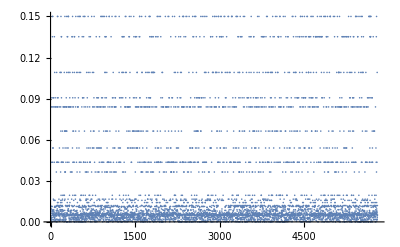

-Graphics3D-

-Graphics3D-

```mathematica
OpacityArray=Array[0&,{L1dimSz}];
Table[
OpacityArray[[SolventCoord[[i]][[3]]-L1dimSz]]=OpacityArray[[SolventCoord[[i]][[3]]-L1dimSz]]+1.,{i,1,Length[SolventCoord]}
];
OpacityArray=OpacityArray/Max[OpacityArray];
OpacityArray=OpacityArray;


PlottedSolvent=0;
PlottedSolvent = Table[
Solvent =Graphics3D[{Opacity[If[SolventCoord[[i]][[3]]-L1dimSz>75,0,1]*.15*OpacityArray[[SolventCoord[[i]][[3]]-L1dimSz]]^4],Cyan,Sphere[SolventCoord[[i]],.55],Boxed-> False}]
,{i,1,Length[SolventCoord]}
];

Outt=Table[
If[SolventCoord[[i]][[3]]-L1dimSz>75,0,1]*.15*OpacityArray[[SolventCoord[[i]][[3]]-L1dimSz]]^5
,{i,1,Length[SolventCoord]}
];

ListPlot[Outt,PlotRange->Full]
Show[PlottedSolvent ]
```